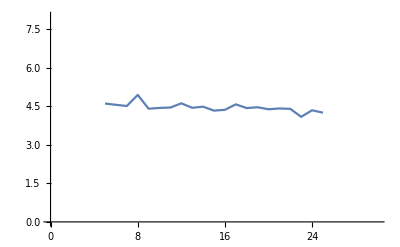

{{5.,4.60917},{6.,4.55917},{7.,4.51333},{8.,4.94583},{9.,4.4075},{10.,4.43833},{11.,4.45333},{12.,4.61667},{13.,4.4425},{14.,4.48667},{15.,4.33333},{16.,4.36417},{17.,4.5775},{18.,4.4325},{19.,4.46417},{20.,4.38667},{21.,4.41667},{22.,4.40167},{23.,4.0925},{24.,4.34667},{25.,4.25417}}

```mathematica
ClearAll["Global`*"]
(*----------2 Rewireing Networks----------*)
(*----------Basic Setup----------*)
n=16; (*SETUP the number of nodes*)
p=10; (*SETUP the repetitions of calculating the average with the rewirewings*)
rEnable=True; (*ENABLES the randomisation (True/False)*)
autoGraphMode=True; (*ENABLES the Auto-Graph function (drwas a Graph from 5-25% of rewireing)*)
(*----------Advanced Setup----------*)
sOutput=False; (*SETUP specificOutput per graph (prints every graph and matrix)*)
debugEnable=False; (*ENABLES the debug mode (more output)*)


(*---Do the rewirewing from 5 to 25 percent---*)
If[autoGraphMode,
r=4;
percentageRewireingList={};
Do[
r=r+1;

(*---Do the Graph p times---*)
rewireRepititionAverageList={};
Do[

(*----------Setup a basic matrix with n nodes----------*)
m=IncidenceMatrix[CycleGraph[n]];
(*Change the structure of the default matrix*)
(*2nd edge*)
m[[n,2]]=0;
m[[2,2]]=1;
(*1st edge*)
m[[2,1]]=0;
m[[n,1]]=1;

(*-----Manipulation of the matrix------*)
If[rEnable,
Do[
(*pick a random edge to change*)
pickEdge=Random[Integer,{1,n}];
If[debugEnable,Print["Edge:",pickEdge]];

(*find a changable node*)
changeNode=0;
For[i=1,i<n+1,i++,
If[m[[i,pickEdge]]==1 && i≠pickEdge ,
changeNode=i;
];
];
If[debugEnable,Print["Change Node:",changeNode]];

(*find a new random node for the edge to connect*)
(Label[newRandom];
newNode=Random[Integer,{1,n}];
If[debugEnable,Print["New Node:",newNode]];
(*check if the changenode is the new node (loop)*)
If[newNode == changeNode || newNode==pickEdge,
If[debugEnable,Print["Same Node"]];
Goto[newRandom];
,Goto[nodeCheck];
];
Label[nodeCheck];
(*check if the new node create only a NEW connection*)
For[i=0,i<n+1,i++,
If[m[[pickEdge,newNode]]==1,
If[debugEnable,Print["Same Connection"]];
Goto[newRandom];
,Goto[connectionCheck];
];
];
Label[connectionCheck];
(*change the connection*)
(*change the connection*)
rollbackChange=m[[changeNode,pickEdge]];
rollbackNew=m[[newNode,pickEdge]];
m[[changeNode,pickEdge]]=0;
m[[newNode,pickEdge]]=1;

(*if the new connection causes a dead end: rollback*)
If[MeanGraphDistance[IncidenceGraph[m]]≥Infinity, 
If[debugEnable,Print[Red,"Infinity_Alert"]];
m[[changeNode,pickEdge]]=rollbackChange;
m[[newNode,pickEdge]]=rollbackNew;
Goto[newRandom];
,Goto[confirmedPoint];
];
Label[confirmedPoint]);
,Round[n/100*r]];
];

(*-----Functions-----*)
AppendTo[rewireRepititionAverageList,MeanGraphDistance[IncidenceGraph[m]]];

(*-----Output per rewirewing-----*)
If[sOutput,
matrixLabel=Table[x,{x,n}];
Print[MatrixForm[m, TableHeadings->{matrixLabel,matrixLabel}]];
IncidenceGraph[m,VertexLabels->"Name",EdgeLabels->"Name"];
m=IncidenceGraph[m];
Print[Table[Graph[m,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}]];
mAverg=MeanGraphDistance[m];
Print[mAverg];
];
,p];

(*Auto-Graph erstellen*)
AppendTo[percentageRewireingList,{r,Mean[rewireRepititionAverageList]}];
,21];
];



(*-----Output------*)
Print[ListPlot[percentageRewireingList,Joined->True,PlotRange->{{0,30},{0,n/2}}]];
Print[N[percentageRewireingList]];
```